```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;m=1;a=1;V[r_]=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];VCou[r_]=-α/r;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefV[r].mx
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefVs2[r].mx
```

```mathematica
GraphicsGrid@{{Plot[efV[[8]],{r,0,10}],Plot[efVs2[[8]],{r,0,10}]}}
```

$Aborted

```mathematica
efV[[8]]=-efV[[8]]
```

-InterpolatingFunction[{{0., 2000.}}, <>][r]

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDATA_δefV[r].mx",efV];
```

```mathematica
evShifted=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
AbsoluteTiming[efV=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V[r],en[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.0001];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

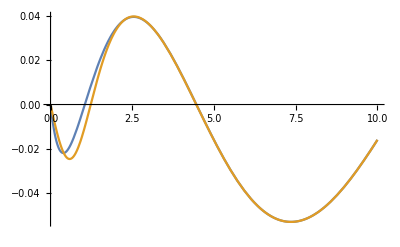

```mathematica
Plot[{efV[[8]],efVs2[[8]]},{r,0,10}]
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Integration1st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
Integration2nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

{-0.0118215080594748838738663280926,0.00023058573157618220175645079752,0.000152021446066631106615979455615,-0.00010004064161802593998564470772,-0.0000712863694187992713985304761932,0.0000538816241427531184846351376787,-0.0000424977198126281860002750737079,0.0000345988322816441319952550152875,0.000028863662218955839508613890068,-0.0000245483620893434848664237598532,-0.0000212070367900866930981914717511,0.0000185583808502047271253166923852,0.0000164172900131842971991399755641,-0.0000146575952810793228084711248025,-0.0000131906947752832573902674923337,-0.0000119527562416834219121189972811,0.0000108967626693679917325890984714,9.98740547446861244276866464333×10^-6,-9.1977122580340387114627734933×10^-6,8.50679262455365161761773821358×10^-6}

{0.0191098016094823241927531442072,0.00751625394121985572891432716918,0.00332666171902297303110403599473,-0.00199746108231531022934924954343,-0.00137211049712140038868463979832,0.00101813887116025132037307383744,-0.000794544988399104629426826331513,0.000642559096416718397967938764931,0.000533652917627960471793201712952,-0.000452442224972107675053244543283,-0.000389962525624778939242148329685,0.00034066877387380483436229132442,0.000300964130866267942268290747546,-0.000268423180298293375067860259981,-0.000241356739469755246412653446323,-0.000218555775273058271496890888365,0.000199134400898135991916448976477,0.000182430171170346697198566248714,-0.000167938821343907597737757056524,0.000155270986568837192724052165512}

```mathematica
ψrTrue[n_][γ_,η_]:=4π(γ Integration1st[[n]]+η a^2 Integration2nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrue[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
γl={};ηl={};
```

```mathematica
Determine[0]
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000131906947752832573902674923337 γ-0.000241356739469755246412653446323 η)==0.014346,4 π (8.50679262455365161761773821358×10^-6 γ+0.000155270986568837192724052165512 η)==-0.00923711}) is less than WorkingPrecision (30.).

{{0,-30.3084907064712654217821530633},{0,-3.07358173374671105987048975006}}

```mathematica
Module[{γη},
γl={};ηl={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γl,γη[[1]]];
AppendTo[ηl,γη[[2]]];
,{r0,0,250,0.005}],Row[{ProgressIndicator[r0,{0,250}],100 r0/250"%"}]]];
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000131906947752832573902674923337 γ-0.000241356739469755246412653446323 η)==0.014346,4 π (8.50679262455365161761773821358×10^-6 γ+0.000155270986568837192724052165512 η)==-0.00923711}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-0.0000131906947752832573902674923337 γ-0.000241356739469755246412653446323 η)==0.0142002,4 π (8.50679262455365161761773821358×10^-6 γ+0.000155270986568837192724052165512 η)==-0.00914332}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-0.0000131906947752832573902674923337 γ-0.000241356739469755246412653446323 η)==0.0140556,4 π (8.50679262455365161761773821358×10^-6 γ+0.000155270986568837192724052165512 η)==-0.00905022}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
γl
ηl
```

{{0.,-154.626134253512128428782678046},{0.001,-154.998474940212035120869402675},{0.002,-155.098485855692726338609279656},{0.003,-154.750585141037447353019169589},{0.004,-154.711945341240457575097196922},{0.005,-154.148362503744474426268286133},{0.006,-153.727731738299065152453471892},{0.007,-153.441582284569942901342500179},{0.008,-153.312020124134494668885719398},{0.009,-152.905525548402068901324964267},{0.01,-152.527155501837080461607122628},{0.011,-152.25917572261506496883686004},{0.012,-151.984273219185193878738722173},{0.013,-151.633052830981911825829372947},{0.014,-151.319514672830585614612419674},{0.015,-150.994224275906443049897168652},{0.016,-150.737504859571724012434235409},{0.017,-150.384672320486433629127894772},{0.018,-150.06641518609938746180523232},{0.019,-149.825046144613183731957384411},{0.02,-149.422467006497358276541366278},{0.021,-149.157245589736412321338704901},{0.022,-148.883877850144999264868070472},{0.023,-148.528758135776515980559195122},{0.024,-148.213378409165033587870200729},{0.025,-147.954420310738873498982995332},{0.026,-147.607354037241014617434617948},{0.027,-147.310957389937597757011774616},{0.028,-147.015865458687982246715801666},{0.029,-146.701691262081866958298596253},{0.03,-146.412866930678443720105015997},{0.031,-146.078233687782522180976518404},{0.032,-145.777650789962701239536979057},{0.033,-145.515943137170378621217095446},{0.034,-145.179338657337096704404924038},{0.035,-144.880035999968680249573499773},{0.036,-144.57394664921075027997633507},{0.037,-144.281805373554820906589816158},{0.038,-143.974729488482627063040942007},{0.039,-143.669269317728788779716271886},{0.04,-143.389027497204490376297218728},{0.041,-143.073994837790797862767812215},{0.042,-142.780150401795901165938810353},{0.043,-142.487229725602045838379767003},{0.044,-142.166248371510550191303902109},{0.045,-141.892633986144270481153423062},{0.046,-141.58364703176781715240133183},{0.047,-141.295930885297820420803549255},{0.048,-140.983169081960541310198160741},{0.049,-140.694223620178655551154335345},{0.05,-140.407278709900839618718490544},{0.051,-140.100267203197067702101098718},{0.052,-139.817272210329222033857573644},{0.053,-139.516162869234242804961310385},{0.054,-139.220785798913257525026729774},{0.055,-138.942222330351895355821014036},{0.056,-138.62434327760948605325243542},{0.057,-138.337176979675202716291281452},{0.058,-138.066077208204687169374768561},{0.059,-137.750342968463374856932991943},{0.06,-137.468182812953884533634035203},{0.061,-137.166137654164485393940560254},{0.062,-136.899958814309855865968682914},{0.063,-136.597578614879294890794383453},{0.064,-136.293639685094765099158920374},{0.065,-136.006977373026113090017695676},{0.066,-135.740314349519547939756766033},{0.067,-135.44157408064780371953813312},{0.068,-135.14359038110897137588225399},{0.069,-134.859664136005170653983640329},{0.07,-134.582535169087377008306655916},{0.071,-134.283977999743367336556496729},{0.072,-134.004735210133941577214852689},{0.073,-133.715304669558617774364042984},{0.074,-133.440925333230447270000398229},{0.075,-133.132928067766789754937128107},{0.076,-132.866831647665645158127676569},{0.077,-132.581563754662625472417959473},{0.078,-132.284261313046324305607210614},{0.079,-132.016452787107294462424570418},{0.08,-131.731275436987771329398705029},{0.081,-131.431834068681247212981265921},{0.082,-131.165615111142444720000461345},{0.083,-130.881903087283039621035753014},{0.084,-130.599673790993181255935880996},{0.085,-130.323436831364487761983352957},{0.086,-130.031754102417680495994491152},{0.087,-129.749557002541599691445285895},{0.088,-129.484420896749488000943102266},{0.089,-129.196939599476429692869199973},{0.09,-128.923704356085956719390388067},{0.091,-128.630669403269718181733598766},{0.092,-128.367432203304565989628565834},{0.093,-128.083739926347646887816928204},{0.094,-127.807449271088233908814754662},{0.095,-127.538324664811699619480220796},{0.096,-127.248544643616749964245833435},{0.097,-126.973807278759526180888568515},{0.098,-126.706202657274856957934542766},{0.099,-126.423525030246162218035551513},{0.1,-126.15765972945953542843940846},{0.101,-125.873748856615208123836911349},{0.102,-125.601345471003460980279198908},{0.103,-125.331092112778176904120528264},{0.104,-125.056712684689081911478991751},{0.105,-124.791898004655183358107639924},{0.106,-124.503750517170603450013515638},{0.107,-124.237649251873580412376401811},{0.108,-123.970550645803001392621987975},{0.109,-123.700002914685008606169083421},{0.11,-123.428676991264135098756735237},{0.111,-123.148312993033090602902108141},{0.112,-122.884727563346601611360730206},{0.113,-122.624325261058858978606480839},{0.114,-122.341374522742456040463877283},{0.115,-122.076881129823568613292575961},{0.116,-121.80822054359879455956407115},{0.117,-121.540915125580020151067642028},{0.118,-121.277694344870109624345373449},{0.119,-120.998415520953934945237990616},{0.12,-120.744470990836759075839070065},{0.121,-120.474305218955132210997084472},{0.122,-120.20831019644781817755694018},{0.123,-119.942520822902931512656333316},{0.124,-119.675934477847022544358130478},{0.125,-119.412357560828086579690308269},{0.126,-119.14959331998687877821568964},{0.127,-118.879380690276166243318106797},{0.128,-118.622116130635344443395903537},{0.129,-118.361932701981338811213377362},{0.13,-118.087114644162116772641680516},{0.131,-117.826488069256583513283744915},{0.132,-117.572918883492642220304536337},{0.133,-117.30249701857674289236740131},{0.134,-117.049305132994606496201386187},{0.135,-116.783243001573824950964984624},{0.136,-116.52030195953116891651153236},{0.137,-116.264350342182968995400588782},{0.138,-116.004221580375049687989803472},{0.139,-115.746702992465744177928134664},{0.14,-115.486191518593298002891313127},{0.141,-115.223199808515415897006611997},{0.142,-114.969616104010602082205531188},{0.143,-114.707184796869950456617641299},{0.144,-114.457691891027040538983109872},{0.145,-114.195288851796295811956265629},{0.146,-113.941691761260335389514796878},{0.147,-113.682801041451345093474401454},{0.148,-113.422348305482304992834175087},{0.149,-113.176431432078615231560771227},{0.15,-112.916262566586718778388402606},{0.151,-112.66221668296055059729525022},{0.152,-112.403816524398130585662219715},{0.153,-112.154229792401916292574810043},{0.154,-111.894952428547178347496684787},{0.155,-111.652303070825713111522432797},{0.156,-111.388415001912603131317487086},{0.157,-111.141772166577141370334837465},{0.158,-110.886743194662605312301250543},{0.159,-110.63509960750143254276948298},{0.16,-110.385727377808109744160742365},{0.161,-110.133285996877858395129431642},{0.162,-109.880395694492531459633285453},{0.163,-109.631881435391698316867339688},{0.164,-109.38341070165504933523527403},{0.165,-109.130058485572380516238414733},{0.166,-108.884547276497949478993088812},{0.167,-108.635375888786374292239145647},{0.168,-108.386706922920603596312708384},{0.169,-108.138333993737685200191673685},{0.17,-107.891688104628138392198681794},{0.171,-107.642202542677768659952270048},{0.172,-107.391680111659439867443806704},{0.173,-107.153610376749795611000668931},{0.174,-106.904712905133231865484964119},{0.175,-106.655000895953757774079240691},{0.176,-106.40787412332365447669735783},{0.177,-106.170478152193917149082280181},{0.178,-105.920425848348155868116642882},{0.179,-105.679159484416675774427691205},{0.18,-105.430829925132781372422443858},{0.181,-105.192350892715838894232476161},{0.182,-104.942179380468252434871883836},{0.183,-104.703252250307813090780689059},{0.184,-104.462190388834655201610086807},{0.185,-104.218928959682940072602075801},{0.186,-103.974163507801176223098950353},{0.187,-103.731070250641741872638843688},{0.188,-103.495910721534939760533382683},{0.189,-103.25240342155449933863473406},{0.19,-103.011333031603312982163284434},{0.191,-102.768599952644744720968035048},{0.192,-102.535318713562301338117072376},{0.193,-102.293857873582612182240521804},{0.194,-102.0507522503711826976970131},{0.195,-101.813324369177034894508937188},{0.196,-101.575417627356141789101282024},{0.197,-101.344173436244027298959451732},{0.198,-101.094708381578452654817559611},{0.199,-100.86270114371019332016562545},{0.2,-100.629624631110974612296648472},{0.201,-100.388718987207668130936877047},{0.202,-100.155766036665227182096281298},{0.203,-99.9170126015298063838950054583},{0.204,-99.6788143986650485665443460093},{0.205,-99.4494875581036965588022513911},{0.206,-99.21262502130912386142245755},{0.207,-98.9785238222408810973263195271},{0.208,-98.7450832482006866141381744748},{0.209,-98.5085815023497813772358536295},{0.21,-98.2754272198079281576830802545},{0.211,-98.0445975403024594858459771306},{0.212,-97.8107690511963969196379309569},{0.213,-97.5795634492265879254735857154},{0.214,-97.3472891757528120784458648264},{0.215,-97.1144861941858266226506673325},{0.216,-96.8810874842468811635983265018},{0.217,-96.6495995247794175553061270435},{0.218,-96.4274633994999521349776828449},{0.219,-96.1889514521707223894172651794},{0.22,-95.9591278612239017413196846649},{0.221,-95.7322999638798563405592927395},{0.222,-95.5036396534884611495885898744},{0.223,-95.2744352495498627866419361079},{0.224,-95.0420563206643257376449773448},{0.225,-94.8173920308539239693472454337},{0.226,-94.5914998296065079949022320789},{0.227,-94.3599731629584782045429792611},{0.228,-94.1338821224318349693897606537},{0.229,-93.909706747695779227014637899},{0.23,-93.6785968518201859469137053134},{0.231,-93.4550563015799980574660390061},{0.232,-93.227272682229616167160275339},{0.233,-93.0047419456716902810931361384},{0.234,-92.7759697676641564475270277041},{0.235,-92.5554498221075798672462646882},{0.236,-92.3276548666877571976195661688},{0.237,-92.1031473085079886083449198179},{0.238,-91.8827556574221114717910244221},{0.239,-91.6551521132748895973554781759},{0.24,-91.4343981025230228467761732132},{0.241,-91.2091135275137057758562016014},{0.242,-90.9930665203318845009890294344},{0.243,-90.7624782145891586545190707988},{0.244,-90.54326970375248220592045169},{0.245,-90.3246730004836121540372780554},{0.246,-90.1014409863578171667150844351},{0.247,-89.8772764812928122672440800338},{0.248,-89.6638231058820425047752009894},{0.249,-89.4382549893780924911099522166},{0.25,-89.2170763273781758540012068998},{0.251,-89.0055884330743776302468716503},{0.252,-88.7791873453710594464239903426},{0.253,-88.5615658276537056071407973216},{0.254,-88.3433453275854558704725571772},{0.255,-88.1241593132737035030522722913},{0.256,-87.908882368334492846243120857},{0.257,-87.6908140268348656935344005499},{0.258,-87.4706106686607649827496752596},{0.259,-87.2577458513253503140383877044},{0.26,-87.0381011541037628897314870757},{0.261,-86.8253087691634277173848433862},{0.262,-86.608431235076993017872641799},{0.263,-86.3902207522615685738227755345},{0.264,-86.1756495999319292557358084373},{0.265,-85.9601999129737535981420077112},{0.266,-85.7481567889677006639185967536},{0.267,-85.5310264708612986972789094214},{0.268,-85.3187626272537421006005853264},{0.269,-85.1059403665868435097244097356},{0.27,-84.890860834612521873601873564},{0.271,-84.6776588847073301058149183058},{0.272,-84.4640772717518231138250600121},{0.273,-84.2569994932016411976989194706},{0.274,-84.0390864079688494854288551329},{0.275,-83.8287252718836210401130834027},{0.276,-83.6186787344743317961703613736},{0.277,-83.406116595584558360108422572},{0.278,-83.1982444001278260425997530591},{0.279,-82.9849647673514336045154192186},{0.28,-82.7742289882095244137218079131},{0.281,-82.5670408176678778578317375248},{0.282,-82.3550434773001910949166165643},{0.283,-82.145220949962713813992614853},{0.284,-81.9397789628849764833587344105},{0.285,-81.7276363708439675491828931113},{0.286,-81.5202941830616022587953794745},{0.287,-81.314348007970096924540967707},{0.288,-81.1064465534674270129323748822},{0.289,-80.8968890762635593124124381476},{0.29,-80.6926133043574720118023515058},{0.291,-80.4835093002883325285732125986},{0.292,-80.2800397693316913084004792281},{0.293,-80.0707626387547824609043737294},{0.294,-79.8673146743536140962546661604},{0.295,-79.6610943902740208374518373665},{0.296,-79.4538795834606024962706425582},{0.297,-79.2520024766490537727756884597},{0.298,-79.0466321535652613341292845897},{0.299,-78.8421639330377848135044360353},{0.3,-78.6371634889619830253829335632},{0.301,-78.4334557598129139307866834773},{0.302,-78.2337530755005346560924124522},{0.303,-78.029462116032019351371188186},{0.304,-77.8242803991584601275358725482},{0.305,-77.6229905863501480365820266148},{0.306,-77.4227718310891298806260794324},{0.307,-77.2187357194453071023303030025},{0.308,-77.0174660896223940395320579118},{0.309,-76.8184502645743351975011583601},{0.31,-76.6170437943729073242504074853},{0.311,-76.4144926307982540441692535935},{0.312,-76.2156508869451609052192885035},{0.313,-76.0158295337462403386435686809},{0.314,-75.81713478599714252461760638},{0.315,-75.6158197042986608780541105626},{0.316,-75.4190145490572672424748305697},{0.317,-75.2185251865997226711006811597},{0.318,-75.0216443443435218817359700294},{0.319,-74.821982399361310681973325497},{0.32,-74.6242989767410897901792530776},{0.321,-74.4284931925150801928820178112},{0.322,-74.2302527231294955718741516765},{0.323,-74.0341876149797184488981136723},{0.324,-73.83730693593734073396061822},{0.325,-73.6416426996481049827977760915},{0.326,-73.4428298157864027963894162301},{0.327,-73.2510659267038224802357292914},{0.328,-73.055159085051895984786818807},{0.329,-72.8564585814587516304470792505},{0.33,-72.6633712277600546171066296983},{0.331,-72.4708930072905632709696958441},{0.332,-72.2748602412642393197390805269},{0.333,-72.0808971933234760529696917706},{0.334,-71.8883077886818378775088864915},{0.335,-71.6950901807550787574197885873},{0.336,-71.5026317754303512794044295691},{0.337,-71.3078510024272448257627377079},{0.338,-71.115774274888127518382968539},{0.339,-70.9238417929439232270094371376},{0.34,-70.7341599507164300332036662302},{0.341,-70.5425621405899749630884761873},{0.342,-70.3479297305839486839953515624},{0.343,-70.1575145564017263749700092502},{0.344,-69.9705620104325311949095725262},{0.345,-69.7776924731556710340510496817},{0.346,-69.5887561734107982864811913713},{0.347,-69.3971378687960171524284987932},{0.348,-69.2080208203160003404718290618},{0.349,-69.0202053191870536190439133881},{0.35,-68.8305514300001018150719065792},{0.351,-68.6431927517650774695998487493},{0.352,-68.452219336299556634621182388},{0.353,-68.2651567397327100578451281214},{0.354,-68.0795555836639765276984692908},{0.355,-67.8907129922897354355572118796},{0.356,-67.7031711788173061453546882463},{0.357,-67.5181776268781846544649388049},{0.358,-67.3284782934744123635606881072},{0.359,-67.1427478029794813888103983926},{0.36,-66.9596337707281623686470535324},{0.361,-66.7725239271389389421780549614},{0.362,-66.5865803971647814556403093613},{0.363,-66.4010331504249674826350248578},{0.364,-66.2178496436996247867473457449},{0.365,-66.0335542732307751208604897321},{0.366,-65.8458669391317993422391157695},{0.367,-65.664987618322041071414266378},{0.368,-65.480838077506993923452749893},{0.369,-65.2968612048961350257288472245},{0.37,-65.1138098626913478676941810884},{0.371,-64.9299609541983371969759633911},{0.372,-64.7491032833645946330259144621},{0.373,-64.5648005844230943305055827353},{0.374,-64.3857420149639155799918045034},{0.375,-64.2024430869225668880248692162},{0.376,-64.0207668608710352719087156674},{0.377,-63.8388445213123050924718608545},{0.378,-63.6594790532278135297649918692},{0.379,-63.4790530537398730636748000554},{0.38,-63.2983067335039282614535355105},{0.381,-63.1181246561915924543067676173},{0.382,-62.937056831389651917013268684},{0.383,-62.7599718546877390348433852922},{0.384,-62.5792979915044108791894257598},{0.385,-62.4001606857499701411067722842},{0.386,-62.2220579503871490718502487835},{0.387,-62.0426006641387351325738796573},{0.388,-61.8663068784447211524220403077},{0.389,-61.6872728724977067565319332131},{0.39,-61.509333509083994136734251552},{0.391,-61.3341808398543114489378211112},{0.392,-61.1569531730926357799926894445},{0.393,-60.9775607861366559458650649668},{0.394,-60.802133755408228417600119871},{0.395,-60.6262293575409011949020036342},{0.396,-60.4521158858172346229730673274},{0.397,-60.2755776891873556197804824701},{0.398,-60.0990290240476213916135963531},{0.399,-59.9234152462386277336229323918},{0.4,-59.7506402073350833193899389256},{0.401,-59.5763965260100233084690567123},{0.402,-59.4020676107705294029533556023},{0.403,-59.2265627499575543216371350277},{0.404,-59.0532841761160735421117494758},{0.405,-58.8812642438714437512706523019},{0.406,-58.7064531667733888718002800025},{0.407,-58.535322458415875012597669859},{0.408,-58.3616731255717519290866331248},{0.409,-58.1893765122104047486293127179},{0.41,-58.0174472968625719449342656512},{0.411,-57.8454039045643295394304421015},{0.412,-57.673787412799390929733008682},{0.413,-57.5035524212669405633388333953},{0.414,-57.3298267154083445417116333011},{0.415,-57.1600166810236565348246852766},{0.416,-56.9928820723941644930678025916},{0.417,-56.8179004100878458384150451083},{0.418,-56.651155410940213408694143668},{0.419,-56.4819136400457891573644023966},{0.42,-56.311016002135515568506064568},{0.421,-56.1414591876193807976635238569},{0.422,-55.9730220828450304980494720563},{0.423,-55.8062088398127573257581123378},{0.424,-55.6353900090235651714251153625},{0.425,-55.4684300489167680141524420346},{0.426,-55.3009995420392796343367035713},{0.427,-55.1329567962871113556894134892},{0.428,-54.964845314397924989832679727},{0.429,-54.7995969328626460375682421494},{0.43,-54.6311473219212494105958063572},{0.431,-54.4649798578169296977115406432},{0.432,-54.3000029508336013266771172149},{0.433,-54.1329417301062557307848578162},{0.434,-53.9678293689535150460364445592},{0.435,-53.8026337895116006351168104151},{0.436,-53.6365790688758927116500780045},{0.437,-53.4731831385952244265735871452},{0.438,-53.306888403195376071816574503},{0.439,-53.143764275363535726705143719},{0.44,-52.9791253954056396138682023348},{0.441,-52.8146799609287092083512191442},{0.442,-52.6515661710878675171415669802},{0.443,-52.4888022102768165325535973045},{0.444,-52.3248137255913981386852749391},{0.445,-52.1614701402700346150226577904},{0.446,-51.999815945385578715406972612},{0.447,-51.8373281713452558126793571106},{0.448,-51.6761698418070762554775092845},{0.449,-51.5125772126415897885881964612},{0.45,-51.3525851995930013904582921998},{0.451,-51.1898336675158392578325807585},{0.452,-51.0296165738021382922129243431},{0.453,-50.8680993008980746096104850855},{0.454,-50.7090717479740150450724747849},{0.455,-50.5474022124617636896747454622},{0.456,-50.3877793360647385166286703642},{0.457,-50.2268073190118284351907761457},{0.458,-50.068289241622996842095129216},{0.459,-49.9105510014398148139942949143},{0.46,-49.7505676487156602586841691173},{0.461,-49.5914507107159800507550207415},{0.462,-49.4320513546412991432891170073},{0.463,-49.2760674928776602025280635154},{0.464,-49.1156633350377985889717385687},{0.465,-48.9592633618939042710694386202},{0.466,-48.801814149531730688787130627},{0.467,-48.6443068473683545918106324091},{0.468,-48.486245886648967785725552532},{0.469,-48.329821968116005473252238094},{0.47,-48.1738413799800886024530516131},{0.471,-48.0188149508801289034657733},{0.472,-47.8598455674701420826802394357},{0.473,-47.7061601361960816655143763952},{0.474,-47.5507009511040548150948196666},{0.475,-47.3948803611940617803488436631},{0.476,-47.24094431695349092560813509},{0.477,-47.0838996460929725381202101233},{0.478,-46.9309127979153712594847871736},{0.479,-46.7775607943978708204138739425},{0.48,-46.6228779431359090032743779355},{0.481,-46.4678527392585704433752395672},{0.482,-46.3143016651317227701606589695},{0.483,-46.1626300040676499168759056121},{0.484,-46.0101698349465106326023089894},{0.485,-45.8552045934449143157203092279},{0.486,-45.7029454591765780629592448256},{0.487,-45.5512576960339031246265878961},{0.488,-45.4004136422560626380030497903},{0.489,-45.2456156347130721799115831124},{0.49,-45.0963080051640835130848657689},{0.491,-44.9452834476665185233499135955},{0.492,-44.7920325774795204169128066544},{0.493,-44.6428992653254135620558644594},{0.494,-44.4909473598324778189412473448},{0.495,-44.3427960631471178552697233126},{0.496,-44.1920471212887588623361659182},{0.497,-44.0395214621047636054592096238},{0.498,-43.8937712190826733334282072682},{0.499,-43.7429220586702923999287258823},{0.5,-43.5915565545140533624592475661},{0.501,-43.4448386256033857155011079493},{0.502,-43.2960809883409587585994494597},{0.503,-43.1483708808201400846702883621},{0.504,-42.9983731574762726815952829596},{0.505,-42.8487024190668621320735899927},{0.506,-42.7054162429050922331354352508},{0.507,-42.5561632113569201443684675797},{0.508,-42.4078225958140797051576402186},{0.509,-42.2611996345974074471419125471},{0.51,-42.1160346354025852254484136098},{0.511,-41.9672382880469494752627132864},{0.512,-41.8222038349563395313884997869},{0.513,-41.676254742910968123087281038},{0.514,-41.5297621487864990678053230499},{0.515,-41.3835885465961010510358875071},{0.516,-41.2403700887052584878101484078},{0.517,-41.0942265220192050608076374128},{0.518,-40.9479745003279448770363782994},{0.519,-40.8052694930401009288589892021},{0.52,-40.6601042425889713219092806476},{0.521,-40.5161198875792132905389922345},{0.522,-40.3709097001015128572157232073},{0.523,-40.2292605787382459617423648088},{0.524,-40.083101049160919308694634576},{0.525,-39.9431300475603183701161689375},{0.526,-39.7983368525195856921557995897},{0.527,-39.6539830863303007174251355758},{0.528,-39.5138195499913474491233881745},{0.529,-39.3727496756452469581179129817},{0.53,-39.2270270983116901940157074021},{0.531,-39.0867906711580155407561848895},{0.532,-38.9468421067275526306832962858},{0.533,-38.8036978313272397451452550055},{0.534,-38.6620546324121381900323365532},{0.535,-38.5222890653788179751348886945},{0.536,-38.3805477182457955532885276146},{0.537,-38.2406843580752819395571711003},{0.538,-38.1002442220027127410628001466},{0.539,-37.9613070453122080125699619536},{0.54,-37.8192018646675084807445035374},{0.541,-37.6810265765827504415501610669},{0.542,-37.5428440758164471704441458024},{0.543,-37.4023783304997244092098492094},{0.544,-37.2635773231743383288621635772},{0.545,-37.1257715318727828237577686509},{0.546,-36.9865384213887610430214700372},{0.547,-36.8480695491090697331959770131},{0.548,-36.7113546130851150985133660888},{0.549,-36.5743689936514427949706080128},{0.55,-36.4337759855953423005015473774},{0.551,-36.2967281035983346401245867589},{0.552,-36.1628650957176569005255526799},{0.553,-36.024566682856568567866723338},{0.554,-35.886141370533396743818989723},{0.555,-35.7522308270724522576166796258},{0.556,-35.6157233226981064975520447073},{0.557,-35.477661157974852867766659323},{0.558,-35.3443620024060268394029232772},{0.559,-35.20823623688786117368600267},{0.56,-35.0728214947202394361853002293},{0.561,-34.9383457029840804968317996286},{0.562,-34.8035957462828995853851053656},{0.563,-34.6665421238663792280644932167},{0.564,-34.5349710713557213785186655778},{0.565,-34.4001077846757067379346581111},{0.566,-34.2668054347116826052055881409},{0.567,-34.1312573659624243829270026758},{0.568,-33.9975556143025878230333103559},{0.569,-33.8670666762627872880059055925},{0.57,-33.7327060686016519679796810114},{0.571,-33.5988898078824788326873709659},{0.572,-33.4669690192602438192142124797},{0.573,-33.3355746907509771302599312836},{0.574,-33.2027850010492936857397747867},{0.575,-33.0713639265708708189337540186},{0.576,-32.9381413838265361245920322438},{0.577,-32.8070323186718073935533014465},{0.578,-32.6768815320236453155522401871},{0.579,-32.5446298207774791660610567629},{0.58,-32.4139634521896596383024964829},{0.581,-32.2834725762221778679702835326},{0.582,-32.1536566299315713674434943038},{0.583,-32.0230263842372871537537446088},{0.584,-31.8933069909766636838907576811},{0.585,-31.7637801704156889768136458269},{0.586,-31.6324921080649117551544008318},{0.587,-31.5049891362150089977653391077},{0.588,-31.3763031625632070159770258777},{0.589,-31.2450485478545297878744526011},{0.59,-31.1183210914490122572159041655},{0.591,-30.9898273851040747928147172187},{0.592,-30.8615006066035806301548648171},{0.593,-30.7326465423399982956254828588},{0.594,-30.6054750341906342538326780161},{0.595,-30.4769278926555475398761537658},{0.596,-30.3504003512104530617388794629},{0.597,-30.2233357407355245835597779213},{0.598,-30.0958464923392617851096742238},{0.599,-29.9697153985844165355332673115},{0.6,-29.84329943066821151218228142},{0.601,-29.7162611518905622008223538377},{0.602,-29.5904941422310400202076591539},{0.603,-29.4642799355451659470223436512},{0.604,-29.3389293430807518967156756492},{0.605,-29.2135627614297536285218795879},{0.606,-29.0867615709107626457757362873},{0.607,-28.9644063585384259704681922855},{0.608,-28.8377520147632288992104157932},{0.609,-28.712953729193546779129890877},{0.61,-28.5890806864657861273777238985},{0.611,-28.4649352038681725954697024506},{0.612,-28.3416493999802753175294425171},{0.613,-28.2169648705407880587414757638},{0.614,-28.0925805949606920953723810645},{0.615,-27.970330048255879053623545566},{0.616,-27.8476207439919509821577277502},{0.617,-27.7239765068129688251658317163},{0.618,-27.6008292407917461811406997032},{0.619,-27.4801896588574566268336995334},{0.62,-27.3553705187916101779674251059},{0.621,-27.2342575840782882387605458109},{0.622,-27.112910443738764334907475286},{0.623,-26.990494389603072333807137543},{0.624,-26.8690827338616577723370168741},{0.625,-26.7472903963253179834610241517},{0.626,-26.6277253563921543458970476591},{0.627,-26.5058299962352568291095959564},{0.628,-26.3840445939642922517615149019},{0.629,-26.2647479693095861422269171588},{0.63,-26.1459079069521904019727487056},{0.631,-26.0228926525796057115705943984},{0.632,-25.9046083727765363981024062875},{0.633,-25.7858864139751773403826728488},{0.634,-25.6643386263225061824702023955},{0.635,-25.5460057450843806822712396891},{0.636,-25.4279012900075746064972702723},{0.637,-25.3075960108925840452166242954},{0.638,-25.1892299805064609891047108977},{0.639,-25.072198047808721502990631109},{0.64,-24.9525832623946880527835636133},{0.641,-24.8343341965429836296366916818},{0.642,-24.7172456625992842220232848275},{0.643,-24.5994639146378646755118995918},{0.644,-24.4822483202758619443897003344},{0.645,-24.3647796329386295955123819273},{0.646,-24.2476437024976377842068283315},{0.647,-24.1318973211134007095026288238},{0.648,-24.0135566594503846346254627098},{0.649,-23.8973255666491184750345754332},{0.65,-23.7820189408113309321194544495},{0.651,-23.6657104581999411194498102945},{0.652,-23.5502702686417424195598366831},{0.653,-23.433468952649428793856739953},{0.654,-23.318378283516155447689785804},{0.655,-23.2032732940879307120428508668},{0.656,-23.089426618585491676743582038},{0.657,-22.9724008412347824125701570719},{0.658,-22.8588303977295537491125374872},{0.659,-22.7450952651852667346707102851},{0.66,-22.6307642828865555926250202304},{0.661,-22.5152251505885840467497672655},{0.662,-22.4022555520995039851596344845},{0.663,-22.2894210962709268733617558826},{0.664,-22.175155753889822527846182654},{0.665,-22.0613471040670678725400773904},{0.666,-21.9494604848683317887483514693},{0.667,-21.836112761316930965576046909},{0.668,-21.7222810642166093822288266054},{0.669,-21.6112235045327316064765895223},{0.67,-21.498797398374911765187967892},{0.671,-21.3873888725243656546315845538},{0.672,-21.2737996064260092068980696188},{0.673,-21.1629085697517987194701753555},{0.674,-21.0512026038290634236558004332},{0.675,-20.9405443943728505309826320541},{0.676,-20.8289719942795627491111258084},{0.677,-20.7175486831916360009046864525},{0.678,-20.6067302129672038242406482585},{0.679,-20.4969647205771363067204098736},{0.68,-20.3866289378050533655854774166},{0.681,-20.2758728385987544730583220743},{0.682,-20.1653284742878114966038710222},{0.683,-20.0572961322296634351378372768},{0.684,-19.9470747154238726422388591075},{0.685,-19.8363565809777260744539006185},{0.686,-19.7291990224764981712650223187},{0.687,-19.6177376173277277016086414151},{0.688,-19.5111858649430952050817625261},{0.689,-19.4019422125863310863136876342},{0.69,-19.2932686456499883337332611209},{0.691,-19.18516894740744352089340118},{0.692,-19.0761932287387843359506436311},{0.693,-18.969955453961231444206968971},{0.694,-18.8614009612372400458963002541},{0.695,-18.7530690202802432888256562312},{0.696,-18.6474657535003953689047774358},{0.697,-18.5388699730502199707131325239},{0.698,-18.4332378485594924214892615854},{0.699,-18.3256879691174777342709511011},{0.7,-18.2185760220369022691329345791},{0.701,-18.1132415738772237428781332274},{0.702,-18.0071759178859658156951292735},{0.703,-17.9013368806144296864156521696},{0.704,-17.79332398613516089696890516},{0.705,-17.6905137953979859687373720181},{0.706,-17.5836880782459436483489313993},{0.707,-17.4788887409448124064666803748},{0.708,-17.3741316279161121655330871628},{0.709,-17.2683413330934456116396333668},{0.71,-17.1631774266524269046851165273},{0.711,-17.0605163794251087848961572298},{0.712,-16.9552471278606887220778007022},{0.713,-16.8511668818711672504037880469},{0.714,-16.7473657169134804753041510062},{0.715,-16.6425137041435325326225654489},{0.716,-16.5400544796449435918042311754},{0.717,-16.436868162742070801438870608},{0.718,-16.3326785842581605185068772115},{0.719,-16.2300730100174010555043104412},{0.72,-16.127829538180847072479436065},{0.721,-16.0233221441302381402853379266},{0.722,-15.9233941317231747829059917693},{0.723,-15.819516786205365729146290956},{0.724,-15.7168561563822354438157226092},{0.725,-15.6157953685213279857199028121},{0.726,-15.5144465076431251845518037259},{0.727,-15.4118571595192261151747474461},{0.728,-15.3110465162159075722370515713},{0.729,-15.2092866843929878179154186334},{0.73,-15.1090891506452449283129114118},{0.731,-15.0074876108317032681305081802},{0.732,-14.9081581395686609463499001218},{0.733,-14.8063112936780661660649452138},{0.734,-14.7060623584626510877762435448},{0.735,-14.6068709231662587186698724876},{0.736,-14.506175532429223937858371159},{0.737,-14.4052273086624914056394558319},{0.738,-14.3078870317989513745108011733},{0.739,-14.2079536923398657217700190751},{0.74,-14.1088370703295933650169028377},{0.741,-14.0086191529962781987316055389},{0.742,-13.9102515044776121857845892478},{0.743,-13.811368035663364434170336454},{0.744,-13.7140115314145733414467043925},{0.745,-13.6144315976369548213462585938},{0.746,-13.5165425707437243837615918544},{0.747,-13.4189132034720644774712868048},{0.748,-13.3209729647607330146548889698},{0.749,-13.2231367188607872469273439197},{0.75,-13.1262072143164559676364301672},{0.751,-13.0283790428956919668644245532},{0.752,-12.9309733129408113334735745215},{0.753,-12.8343007002560996785385223721},{0.754,-12.7374251984527516585509028695},{0.755,-12.6417103171658823592666383853},{0.756,-12.5453116929460167245853282345},{0.757,-12.4478567178138287193829173415},{0.758,-12.3519863093694258643157461968},{0.759,-12.2577376566575480031752243296},{0.76,-12.1604974782199780998090021856},{0.761,-12.0653004935036131924131680353},{0.762,-11.9693258442580713386649717073},{0.763,-11.8753776334654006611146543031},{0.764,-11.7803716736823238151088325875},{0.765,-11.6842815807393261212595902209},{0.766,-11.5905402180486555080328807676},{0.767,-11.4956025849263293916454923685},{0.768,-11.4025784664497289496357966277},{0.769,-11.3076295742486252561708938185},{0.77,-11.2122728828426122828998012864},{0.771,-11.1202445855481113715121377343},{0.772,-11.0266651554106115870056692832},{0.773,-10.9321547246052564982489027009},{0.774,-10.8391862852292413250247201235},{0.775,-10.7464699336891306569913273849},{0.776,-10.6542718931917536581588778395},{0.777,-10.559532173248712482557410565},{0.778,-10.4687346095183753233691627706},{0.779,-10.3751763438073337984026956749},{0.78,-10.2842637644596672170815277209},{0.781,-10.190947185333816682113398771},{0.782,-10.0989067535763021402720488254},{0.783,-10.0084613524306410953576752765},{0.784,-9.91595621614494260087558764294},{0.785,-9.82415027585203909664309407183},{0.786,-9.73426023078872897873572438754},{0.787,-9.64198831672026568868949245929},{0.788,-9.5520888817886721725031044472},{0.789,-9.46135268474660861957518967954},{0.79,-9.36950496470805067317718645722},{0.791,-9.28022394676221054072805055036},{0.792,-9.19025527293670224124999731608},{0.793,-9.09892735910572929087357249846},{0.794,-9.01044526318555713155446418868},{0.795,-8.92077920995660014398437731419},{0.796,-8.8297654368530632346871136264},{0.797,-8.74085686036060500858370559091},{0.798,-8.65232301653136656853704779356},{0.799,-8.56318113054392882920783437154},{0.8,-8.47451315366531912125713435471},{0.801,-8.385528210972089083238135228},{0.802,-8.29653367860262546985423258339},{0.803,-8.20901065512220239059926051949},{0.804,-8.12070081101641022945685637225},{0.805,-8.0317526529453347155027644011},{0.806,-7.94477712569981420806895618925},{0.807,-7.85762685938553401551361790669},{0.808,-7.76924345108923593704710488572},{0.809,-7.68126140535676256331277773816},{0.81,-7.59490501261005706251877543795},{0.811,-7.50769500008735814712378025457},{0.812,-7.42143754773015354532606224425},{0.813,-7.33292612277922583766986717514},{0.814,-7.24811745094115015073900618071},{0.815,-7.16106137940420869323490527588},{0.816,-7.07424231877049869225715936669},{0.817,-6.98942834410736808491741814212},{0.818,-6.90213574820760702326545404646},{0.819,-6.81751410926934514996683604166},{0.82,-6.73225475840794785001725839348},{0.821,-6.64547102618521414616766759586},{0.822,-6.56079754904575244990976075591},{0.823,-6.47641367421951058529989960613},{0.824,-6.39101966494705732861650064721},{0.825,-6.30605723841775704079944532532},{0.826,-6.22145873059432751420818069117},{0.827,-6.13804994415050905053892949526},{0.828,-6.05204363451023395199349020839},{0.829,-5.96858693282503385662385940325},{0.83,-5.88590736870790508797123460247},{0.831,-5.80148552018787149119637146916},{0.832,-5.71651783049579706462389534774},{0.833,-5.63424059601247228059996721221},{0.834,-5.5514709323641489796819728733},{0.835,-5.46665451899826338679559717035},{0.836,-5.38454450781649165760580625354},{0.837,-5.30266871447147187477954901034},{0.838,-5.21886943585721946649779466713},{0.839,-5.13617395632830579974009688098},{0.84,-5.0541823062025373338236751139},{0.841,-4.9728163204426246465888985476},{0.842,-4.8902192381080855000279666002},{0.843,-4.808065004011886287925594338},{0.844,-4.72663588439395457220299545674},{0.845,-4.64489358404805136930590151539},{0.846,-4.56317312840113506611312777344},{0.847,-4.48324576912391097971510779256},{0.848,-4.40109058413699037205715649226},{0.849,-4.31925323187375993703905632098},{0.85,-4.23993816912605580982807096957},{0.851,-4.15971502580486553136403770263},{0.852,-4.07781477118118109281385130748},{0.853,-3.99848615875488728747789953203},{0.854,-3.9176483436079647761074847487},{0.855,-3.83790067600734684460732315707},{0.856,-3.75877401424600143762218380255},{0.857,-3.678440413082771171049950887},{0.858,-3.598680685685212068051911799},{0.859,-3.51960440107564506524083965372},{0.86,-3.44086628911234074302810414359},{0.861,-3.3609970870349520542355593985},{0.862,-3.28333421742698694549139734377},{0.863,-3.20379668457273275892864587287},{0.864,-3.1245170224942734902797436295},{0.865,-3.04651974783992646871642933743},{0.866,-2.96886090996029618550843702073},{0.867,-2.89095453993997722239763223427},{0.868,-2.81165162660652756364712983525},{0.869,-2.73446482765280048953261845612},{0.87,-2.65703743238160958106865466501},{0.871,-2.57948569336298571001406223519},{0.872,-2.5016285652232734888039473491},{0.873,-2.42525280064138247306156108489},{0.874,-2.34795244424634415635738333284},{0.875,-2.26999070637568654762218792934},{0.876,-2.1946036345996878480094386204},{0.877,-2.11723600005457300539012099811},{0.878,-2.04123605875538626683730285066},{0.879,-1.96513980655523848161093235542},{0.88,-1.8879394908508058084115785566},{0.881,-1.81343306143802246054089376101},{0.882,-1.73614400096972712712824831543},{0.883,-1.66204871076730147021343173705},{0.884,-1.58537270560752243208339085134},{0.885,-1.5103525071121635146976653845},{0.886,-1.43558970354681033958829062695},{0.887,-1.3598205821002904406351571586},{0.888,-1.2847081620976896189614181336},{0.889,-1.21065045657969262619079883468},{0.89,-1.13586979520452295400440959291},{0.891,-1.06111138149190542968346047136},{0.892,-0.986733872313156925932576867611},{0.893,-0.91222367312642395487763012519},{0.894,-0.839323145328489289538119388471},{0.895,-0.764484376728000201918357034274},{0.896,-0.69072146739070295553139388924},{0.897,-0.617817172536012301266002475449},{0.898,-0.543269685023552285316286149876},{0.899,-0.471229300029702543195186044568},{0.9,-0.397207931336635960275636645096},{0.901,-0.324031924954250701606698518865},{0.902,-0.252480016934216017364365592158},{0.903,-0.178524805146428923467925715666},{0.904,-0.10571350122989014686104995203},{0.905,-0.0350810909016043732196601451992},{0.906,0.0381646017980892509699017776979},{0.907,0.111155512627273457803225033523},{0.908,0.182375393610193419437232950873},{0.909,0.253485008784315098438985035251},{0.91,0.325389976908118634765085870701},{0.911,0.397437140769726362384863734675},{0.912,0.469165567714933278670417708265},{0.913,0.540247796255063476621613993161},{0.914,0.610483132484022828225379150779},{0.915,0.68101800944633394700641008653},{0.916,0.753502706865028343869695794635},{0.917,0.823168454222742948813353415295},{0.918,0.89387426461203898105791692986},{0.919,0.963870064682652543701953863746},{0.92,1.03423236065692281780883523511},{0.921,1.1045342162925493797924047175},{0.922,1.17411194053049066426896045949},{0.923,1.24448749507363551779739474217},{0.924,1.31376920315325826169861439751},{0.925,1.38390372733832153141526751507},{0.926,1.4520116571959495642375569592},{0.927,1.52205058797150580373365130969},{0.928,1.59116678753491677631251583788},{0.929,1.66033832914728206652586551756},{0.93,1.72815416642034579321195235215},{0.931,1.79691368663774576561247478522},{0.932,1.8667211976967146418502817963},{0.933,1.93330368668829960592657992212},{0.934,2.00217322231489126695576287068},{0.935,2.07087552425653526810777262612},{0.936,2.13767317712112544226410545291},{0.937,2.20645285831168639588823489189},{0.938,2.27416686000395178438393897205},{0.939,2.34148764892621650379296099326},{0.94,2.40813840182715589654049603521},{0.941,2.47564399507702389840768219559},{0.942,2.54325463243546190926080677991},{0.943,2.61051112773103500329540453299},{0.944,2.6760464232395073574368623354},{0.945,2.74339584555313302488535590736},{0.946,2.81002738539081831266512964562},{0.947,2.87602739608121033171509400719},{0.948,2.94294434980438952741500053397},{0.949,3.00784394797430516912747668555},{0.95,3.07453877314111895847748410837},{0.951,3.14058837810432776078233193416},{0.952,3.20632741722637604912841156344},{0.953,3.27118907354459853808131195816},{0.954,3.33653926203130348430724065787},{0.955,3.40204298458092435344984145776},{0.956,3.46759121981044019126529344192},{0.957,3.53169092652355143045482689021},{0.958,3.59724113825748970205195772525},{0.959,3.66194117270781746838108059329},{0.96,3.72685443660894636340909870885},{0.961,3.7908839560151037191708943397},{0.962,3.85475652570901265389332018708},{0.963,3.91881010084430021468243459447},{0.964,3.98396523016581629327596003464},{0.965,4.04649953617257563186621971026},{0.966,4.11109627487594849939538757577},{0.967,4.17438086015918788448984194539},{0.968,4.23802663997401531510168416913},{0.969,4.3010597263006801786801616632},{0.97,4.36371823817367825526634465315},{0.971,4.42826233486684042237003934474},{0.972,4.49023734708897533893285767709},{0.973,4.55290955053677255479091220536},{0.974,4.61627945027414658494199823515},{0.975,4.67853674034423281770000977914},{0.976,4.74051047692305101188423993021},{0.977,4.80243330774037364337176808794},{0.978,4.86616796481943266077395429878},{0.979,4.92680733748389333453305414744},{0.98,4.9886702868893326229601192231},{0.981,5.05038646545918635828080839277},{0.982,5.1132603230788101769995500619},{0.983,5.17324819669995652019781737929},{0.984,5.23487061008026299363348066011},{0.985,5.29547720809586481043981318294},{0.986,5.35817213302105158351578438146},{0.987,5.41761086785536910975959092691},{0.988,5.47802306653702947180084165826},{0.989,5.53981393298219427839672828501},{0.99,5.5997765143722635015970731353},{0.991,5.65978157112432647330119626934},{0.992,5.72089605445725021106366376421},{0.993,5.77983299936650368713583262583},{0.994,5.84095728767627525613026303667},{0.995,5.9009042091138029637661841164},{0.996,5.95994815067738029550053088064},{0.997,6.01904748565352742623433853669},{0.998,6.07976002005892544913961881492},{0.999,6.13777366356673779281109949201},{1.,6.19793188286364006347615098494}}

{{0.,6.00403049801405564877431806067},{0.001,6.20035470975964985680651544763},{0.002,6.31396895737231251954947451478},{0.003,6.2915818806948086492582208783},{0.004,6.36285805064442557274168162805},{0.005,6.27476827945353303989797178357},{0.006,6.22989770236651751341545036807},{0.007,6.22567723000888781524325986954},{0.008,6.26881226267990010873853751309},{0.009,6.22780853627762550839022137793},{0.01,6.19519568986838677746603558627},{0.011,6.19592668550308876176712931628},{0.012,6.19441857987314214176216384027},{0.013,6.16962279000959656691696942018},{0.014,6.15611789764000552053453763568},{0.015,6.1389097643501757051069044455},{0.016,6.14236214820437445264613277517},{0.017,6.11652357279827251317670105588},{0.018,6.10103452090723397945720848344},{0.019,6.10872945490487363816439099845},{0.02,6.06738905232066527059335118814},{0.021,6.06757467562945626457685722808},{0.022,6.06515251125799434872798831365},{0.023,6.03779685188079155653541765883},{0.024,6.02235868984894032958216898229},{0.025,6.02389811574050767363216467454},{0.026,5.99857681928205518525474613127},{0.027,5.98848890468004978977808252052},{0.028,5.97866132571912575696074774843},{0.029,5.96291057526357055223096359543},{0.03,5.95471397632647480115893184447},{0.031,5.9324880000991235796812673135},{0.032,5.92045566853263998223426711702},{0.033,5.92008070061428835506765775205},{0.034,5.89685416869958895861574348256},{0.035,5.88480822689311376660936386971},{0.036,5.87057025277625408364965408831},{0.037,5.86042971964645585299035491034},{0.038,5.84562621288580118386551101354},{0.039,5.83117998568584783830969319513},{0.04,5.82425038696016829481325594807},{0.041,5.80663575850193141523655902354},{0.042,5.79531581479502540995160626147},{0.043,5.78414420404800716313860026059},{0.044,5.76432964524730066481267124653},{0.045,5.75875096535851741761369412664},{0.046,5.74231197044325883498005658474},{0.047,5.73219387154343687312179910774},{0.048,5.71434826274501322917519400567},{0.049,5.70359611874724763887557582569},{0.05,5.69332053866975736246064768203},{0.051,5.67682837970331701092434671024},{0.052,5.66749109037946906597286105596},{0.053,5.65252983291512432054860621838},{0.054,5.639177954384405754935559639},{0.055,5.63079685441974506180585342273},{0.056,5.61036174440898627353216290162},{0.057,5.59911373641483607600258107656},{0.058,5.59261058608149138074402818385},{0.059,5.57244078963503041224949901328},{0.06,5.56232666723833510369005060701},{0.061,5.54605331808412121381879328019},{0.062,5.54053136984108832171962214719},{0.063,5.52390159239716476302430484954},{0.064,5.50667195713286978347248330655},{0.065,5.49455579544366460567422146628},{0.066,5.48837916649150537212669341985},{0.067,5.47234652079350050218526951766},{0.068,5.45641718120943128413421691571},{0.069,5.44462577282303600172320822094},{0.07,5.43477037163956289140024968427},{0.071,5.418289890238017134527153126},{0.072,5.4075425245895492473473747873},{0.073,5.39357995491858988770068018958},{0.074,5.38405784070290922159191227884},{0.075,5.36421415633722374923474081599},{0.076,5.35695535577722694874855230058},{0.077,5.34375729811912236475897244306},{0.078,5.32678496170471912135137645166},{0.079,5.31863491202302435429574939184},{0.08,5.305093033757060339380964485},{0.081,5.28710128822163208931434602348},{0.082,5.27906340005770587643604895075},{0.083,5.26559664650654590432117349975},{0.084,5.25245695058488942192226476395},{0.085,5.24101237457139365065768299121},{0.086,5.22476056038810763554484764411},{0.087,5.2112638743361233123265872212},{0.088,5.20282027767676839900826554178},{0.089,5.18747736156810416814537904891},{0.09,5.17633413741709654239595754058},{0.091,5.1590641103582418283174732088},{0.092,5.15071131613119027178403561687},{0.093,5.13603335722701614794571625265},{0.094,5.12347989449962463349228228961},{0.095,5.11297968501536552413384494098},{0.096,5.09609417650245631707130978251},{0.097,5.08365146131705301672826156121},{0.098,5.0732525265357213233280976794},{0.099,5.05816216845254535119425716943},{0.1,5.04805200408648657547351080472},{0.101,5.03234919895751768485689593099},{0.102,5.02001794806256816337917985827},{0.103,5.00822016880904380158486721842},{0.104,4.9950524122358738720405386972},{0.105,4.98466756213592250463440494099},{0.106,4.96708739008740706760002552173},{0.107,4.95607639738872555426216024244},{0.108,4.9446452522630027858215877251},{0.109,4.93205048830815736532552447223},{0.11,4.91910245315538106835347033053},{0.111,4.90329597642630292507673415221},{0.112,4.89246192532622060164098052534},{0.113,4.8824767554673874624118090511},{0.114,4.86553581263135665015482986943},{0.115,4.85407710819650477117931496712},{0.116,4.84123840498560691821876348763},{0.117,4.82869493872787595976271148687},{0.118,4.81727480904736811558984076063},{0.119,4.80086857089417929949257318288},{0.12,4.7920314831124972417737472288},{0.121,4.77815918651269786340568278898},{0.122,4.76543714743395021811578144009},{0.123,4.75266287730439484436756431281},{0.124,4.73953246189914496054134757344},{0.125,4.72720065096005040705232262031},{0.126,4.71500132744553460058086780295},{0.127,4.70042895603427585832473544301},{0.128,4.68967035591554164284015506482},{0.129,4.67791298930675255773493101798},{0.13,4.66160344707689440957155115813},{0.131,4.64948541633950353776285300597},{0.132,4.63939519100895413895009296179},{0.133,4.62408060253459862046466897017},{0.134,4.61387974424138979106276125343},{0.135,4.59966285821784507216769641569},{0.136,4.5862806054455523485090476557},{0.137,4.57490651735382782548449299476},{0.138,4.56215376152901098943183152347},{0.139,4.5500812499744014426558444012},{0.14,4.5369896643754697987671870154},{0.141,4.52303469342246529261849370243},{0.142,4.51182245203064515302034301648},{0.143,4.49781586979509498353419612338},{0.144,4.48762323446650922977598592811},{0.145,4.47340440043729950772533194005},{0.146,4.46174644613352083263287062997},{0.147,4.44837290019696975794076754132},{0.148,4.43441581960674405104870102131},{0.149,4.42475817712009069479315094935},{0.15,4.4106682754030449158998706903},{0.151,4.39832640824805812399666917456},{0.152,4.38455481919920785438077357683},{0.153,4.37334770282906172755709920655},{0.154,4.35909262517011790430770584494},{0.155,4.34977270134555458062022312838},{0.156,4.33390244556087012224249522564},{0.157,4.32315493384775278282215888625},{0.158,4.30975588586115556885890801988},{0.159,4.29727600684405541327309586768},{0.16,4.28537757743476834631527797361},{0.161,4.27244090824783106980612908886},{0.162,4.25926094816029849797577566607},{0.163,4.24730138241710075349887239824},{0.164,4.23524826273673157091747597721},{0.165,4.22160792741619331959561636615},{0.166,4.21023952532427786126613743762},{0.167,4.19765471815137409113313421684},{0.168,4.185116282093199885694638937},{0.169,4.17256179917226001225775215076},{0.17,4.16042550116820424248486930255},{0.171,4.1473224016785535635468539557},{0.172,4.13379950568920369012161607558},{0.173,4.12394862783991220060678582132},{0.174,4.11070856473101461316863603078},{0.175,4.09711668445552580716307587423},{0.176,4.08420438113015146931665547581},{0.177,4.0741392158832336089829539952},{0.178,4.06013093785230907199724865871},{0.179,4.04868356226008763700152295344},{0.18,4.03498993306733533382091711341},{0.181,4.0241804720568161557125069514},{0.182,4.00972096641808670590001163703},{0.183,3.9985687664678495958687155871},{0.184,3.98666591792980214002792634817},{0.185,3.97399293166122879025255966708},{0.186,3.96076095583887790099019713362},{0.187,3.94793357196553145958503148984},{0.188,3.93741019434407658164821116124},{0.189,3.92425252001530184501937775897},{0.19,3.91173191658383241138823367238},{0.191,3.89860507504576129499109849522},{0.192,3.8882434113042194367157604334},{0.193,3.8752991588323953290413247189},{0.194,3.86175462209564175957799669133},{0.195,3.84983103144680234660700680778},{0.196,3.83766114913181999957797826188},{0.197,3.82741126965436290247803145941},{0.198,3.81153396768896667410026678543},{0.199,3.80085141642612993307070173715},{0.2,3.78974417964979849421687431471},{0.201,3.7761620399292144883695777602},{0.202,3.76489208664228078984752396426},{0.203,3.75176289851235041238004676567},{0.204,3.73870245213950958234953707547},{0.205,3.72823335322356184669406763753},{0.206,3.71537920864611038763964935453},{0.207,3.70326346810754641673368737876},{0.208,3.69124911605677315448385081726},{0.209,3.67820743194067229715078426009},{0.21,3.66608244149883483236321994228},{0.211,3.65456406070879232451185544137},{0.212,3.64203776848029223035131181339},{0.213,3.63020889668372255005159898166},{0.214,3.61795789496500572063095150194},{0.215,3.60544871123371343228355346679},{0.216,3.59266118374846913539885082539},{0.217,3.58035574013674986899037565325},{0.218,3.5707895642639414101705026022},{0.219,3.5561591498845733130832819915},{0.22,3.5440670894753325031512487112},{0.221,3.53278685872081991334161308145},{0.222,3.52085416878990098266439874431},{0.223,3.50865995525409974246958122745},{0.224,3.49540652404133865147020319757},{0.225,3.48439692308866321116303982295},{0.226,3.47291887570536732963176553498},{0.227,3.45963595619544367358982312888},{0.228,3.44790609020805012855443348131},{0.229,3.43666177160791355999594454028},{0.23,3.42321873804128296708018059764},{0.231,3.4119764415153474214062687903},{0.232,3.39935212080021957872638510074},{0.233,3.38822623446313803208086084024},{0.234,3.37511250337026135838745156466},{0.235,3.36440728661675156535139742808},{0.236,3.35140104612193508447412169451},{0.237,3.33929771473838879104797255365},{0.238,3.32834875468205606340976236288},{0.239,3.31511839512200102773772081462},{0.24,3.30387188502390231932810900466},{0.241,3.2911575901590539779519610792},{0.242,3.28115179730528740948099091745},{0.243,3.26664209669028871929823861305},{0.244,3.25549099153643224787593524636},{0.245,3.24443251074741684148591300613},{0.246,3.23187526416525868639517222547},{0.247,3.21894254249032575168129590857},{0.248,3.20916622723938469036439935423},{0.249,3.19562296798420064627075269675},{0.25,3.18331894757910824335690852312},{0.251,3.1738623079942725919310485072},{0.252,3.1597903703602259402220923613},{0.253,3.14828974167069493524564363293},{0.254,3.13651588939703336380735817033},{0.255,3.12435779251789948414914682309},{0.256,3.11329415659603430865857178125},{0.257,3.10129276116155180683570814004},{0.258,3.08855285230419975572135349943},{0.259,3.07794808820887595469995375085},{0.26,3.06519624520851041300376072337},{0.261,3.05443237140181735395510082779},{0.262,3.04233908609256474187257201588},{0.263,3.02975133489599291280246558649},{0.264,3.0181774539337350847087662571},{0.265,3.00624724345764587111553515557},{0.266,2.99526060416931517380395050737},{0.267,2.9826413744882849538078457373},{0.268,2.97140883654998193988278946019},{0.269,2.95991767163803412897381812199},{0.27,2.94765273650141545848242327888},{0.271,2.93586835858598193105405632218},{0.272,2.92388002383748061141631999541},{0.273,2.9137757735168114817971126466},{0.274,2.90029647615207929310045645146},{0.275,2.88901947425527072949557294036},{0.276,2.87774969496194642641411664376},{0.277,2.86562883499927889144554199812},{0.278,2.85484261715246660867530565393},{0.279,2.84232846785493035151490741948},{0.28,2.83049830784653809304374348773},{0.281,2.81965674195122442772315754199},{0.282,2.80726915251872743535738786176},{0.283,2.79545405709490139227922140798},{0.284,2.78488064000332450988030674348},{0.285,2.77218793213506311440195708669},{0.286,2.76086454751126552699361069415},{0.287,2.74987801726374179764252776614},{0.288,2.738211978297146640531295924},{0.289,2.72595734594040391745412139014},{0.29,2.71521860587345432291833961256},{0.291,2.70292937255336606361638577081},{0.292,2.69226332165536766215897197751},{0.293,2.67975000592954717861154347812},{0.294,2.66891921469278713354213380901},{0.295,2.65716210247981606741850254128},{0.296,2.6450180512158786723203018815},{0.297,2.63440788379202365567571642516},{0.298,2.62265316346644885052997755948},{0.299,2.61108721396375280569073518949},{0.3,2.59927512005167099164455151816},{0.301,2.58777056121473102328601763423},{0.302,2.57739637883986303037537936617},{0.303,2.56554620218462146673107707078},{0.304,2.55334169772707572022432791834},{0.305,2.54223367575861863197232749631},{0.306,2.53136666227980654915866623179},{0.307,2.51925805174746323873739119887},{0.308,2.50790498374670414409091661569},{0.309,2.49715209380916271137570893839},{0.31,2.48559077438286309770728307677},{0.311,2.47359908499468944310696294729},{0.312,2.46264950670020138771050951472},{0.313,2.45131990949452276902772797298},{0.314,2.44024928574453392079013971931},{0.315,2.4283012580780162008628470633},{0.316,2.4176387039226621035371749007},{0.317,2.40577632945087991271711141022},{0.318,2.39492629081370011867926367485},{0.319,2.38315063501896425152767995455},{0.32,2.37189318111016496259200680994},{0.321,2.36112346594906833213092024281},{0.322,2.34953361894229183540890831355},{0.323,2.33852208839670303840592561973},{0.324,2.32718180557093981895549186402},{0.325,2.31612925344623554241804478751},{0.326,2.30404055528193787534478125823},{0.327,2.29400897915172622412744970678},{0.328,2.28263993632732892897238227489},{0.329,2.27034282631624173533078929508},{0.33,2.25966772455684245601892957488},{0.331,2.24909695492780590903306364812},{0.332,2.2373677310152800093438648741},{0.333,2.22618612938890171997120623508},{0.334,2.21534115130426979862029783587},{0.335,2.20422573313112826164237352613},{0.336,2.19326083369618670493527594536},{0.337,2.18151188878931580781241551502},{0.338,2.17050363467528834313815184019},{0.339,2.1594597692290569345887369848},{0.34,2.14901933266901698831910395611},{0.341,2.13791864799362004214986049924},{0.342,2.12581854511085021622694469053},{0.343,2.11491877071676693879486245032},{0.344,2.10499056952939941802662187419},{0.345,2.09318906103938379173072159674},{0.346,2.08250213171589523912604751497},{0.347,2.07092338706532403848259095891},{0.348,2.06002513576447861044640539669},{0.349,2.04944361393869951340797518267},{0.35,2.03822655099839908341615702279},{0.351,2.02762787308235951666442367866},{0.352,2.01585511322483127841976638515},{0.353,2.00519104016036480944809503288},{0.354,1.99489284100487941060506066526},{0.355,1.98353417536518565752935671016},{0.356,1.97249290840131087004743747694},{0.357,1.96214755286818109087176936648},{0.358,1.9502979516601570088802648329},{0.359,1.93957540565400651430803216907},{0.36,1.92956983895401492663217072511},{0.361,1.91827575544677795538195054596},{0.362,1.90725904953166205262749882354},{0.363,1.89628628339074461247632644815},{0.364,1.88595434925354760463247500719},{0.365,1.87520915859433197469112467145},{0.366,1.86335924100082659241391561809},{0.367,1.85349856300613450923969509549},{0.368,1.84257033623047580254928031573},{0.369,1.8316189772739728202026595263},{0.37,1.82087296806792362612854649141},{0.371,1.80980978637339396105407093637},{0.372,1.79957877071588132681040397096},{0.373,1.78822780740149977961733133663},{0.374,1.77839260202243646516012249822},{0.375,1.76719645845748398724943731625},{0.376,1.75641787456089990414039134402},{0.377,1.7454901275266194052678899521},{0.378,1.73526353746205300192785783702},{0.379,1.72464100234701954802306910294},{0.38,1.71384716438772992403046126074},{0.381,1.70315045049327437282883802924},{0.382,1.69211117409225651502184636814},{0.383,1.68220619191090198626867197059},{0.384,1.67113897916129030228591331408},{0.385,1.66046429894947677003525400139},{0.386,1.65003001069526596623217602455},{0.387,1.63911157101989449934069842641},{0.388,1.62907950903779792174016438171},{0.389,1.61814323815057877068199251778},{0.39,1.60746606332636491071875358877},{0.391,1.59756133522533712864464314354},{0.392,1.58695453320451011683672924949},{0.393,1.5756185625140698445144074835},{0.394,1.56541290781641699146754930692},{0.395,1.55499012862799857440994109089},{0.396,1.54503835921328523141118052871},{0.397,1.53427903386884124748026035753},{0.398,1.52344455972489764251484583573},{0.399,1.51282179909840269099952512124},{0.4,1.50298834350178088473860397691},{0.401,1.49263780288127457495431077345},{0.402,1.48218990834822460294937760918},{0.403,1.47131394457889281460460399861},{0.404,1.46104198877159327808789922295},{0.405,1.45108065344465181803266045462},{0.406,1.44020168074038260242384402904},{0.407,1.43036811669354847918808651778},{0.408,1.4196998090165323616721424723},{0.409,1.40937112397584326484680740471},{0.41,1.39908331153835945887596815092},{0.411,1.38869041705376207426970044334},{0.412,1.37835667498443313789606157308},{0.413,1.36837174848675319690537475353},{0.414,1.3572579204128745540454014188},{0.415,1.34726179906458542676891979737},{0.416,1.3380073099237316487664654868},{0.417,1.32630290579997280313968416882},{0.418,1.31702718870573294233152571177},{0.419,1.30692462435253304640062268165},{0.42,1.29625038865386712163569064318},{0.421,1.28591354682141371079384232103},{0.422,1.27584714461632141419307378651},{0.423,1.26620421402431352953302858415},{0.424,1.25527735250979773324823397986},{0.425,1.24545210816600525485827675319},{0.426,1.23541540171162866972414212825},{0.427,1.22512436789707774724257634116},{0.428,1.21474397348400581161484480661},{0.429,1.20516361065091122996868135847},{0.43,1.19454396843958963625164345453},{0.431,1.18454836762702011007191148853},{0.432,1.17484582050115805956246714415},{0.433,1.16444310975970432092528397547},{0.434,1.15456368231224366006307116126},{0.435,1.14459128246153709256194772776},{0.436,1.13429066924681526104438549191},{0.437,1.12472900665404949602352989645},{0.438,1.11422068395239679960219808258},{0.439,1.10460677595511898990668184794},{0.44,1.09446623670969319140387995685},{0.441,1.0843173037634348821268518237},{0.442,1.07450532343439430338376148219},{0.443,1.06473260231478275915710617429},{0.444,1.05452171932171018390134747623},{0.445,1.04443981391284013742767393791},{0.446,1.03480380822718034249633753785},{0.447,1.02484854767503821009864956964},{0.448,1.01523022553882485322701904695},{0.449,1.00480733706408264823807937218},{0.45,0.99541049133116488585640296796},{0.451,0.985110649973762451898460397471},{0.452,0.975513675365867415229055942888},{0.453,0.965456564757508804394822792976},{0.454,0.956088971570114080533527834572},{0.455,0.945854462888885806519236127837},{0.456,0.936175296913752280568611533708},{0.457,0.926021571637090959698417809101},{0.458,0.916546937793471031918369890933},{0.459,0.907243715498909348269667485859},{0.46,0.897194487813606506930628635674},{0.461,0.887343144116456143279755690889},{0.462,0.87734132791310282552507415786},{0.463,0.868310789609210196424821608092},{0.464,0.857874894919893476163386390321},{0.465,0.848589049125602494437031092393},{0.466,0.83892056056416110228147854572},{0.467,0.829170167815883064087244693691},{0.468,0.819187660266326186662171834857},{0.469,0.809637622131527434032623148034},{0.47,0.800158082778335676100640224933},{0.471,0.790904089895582206144608390194},{0.472,0.780390362566571791251121125023},{0.473,0.77141569505467750782122023581},{0.474,0.761839458534167881799038997618},{0.475,0.752090147678859897274102368673},{0.476,0.742849103662749099648386505375},{0.477,0.732601908192257708066437282775},{0.478,0.723522379997176731916822788597},{0.479,0.714269050838405424230047109013},{0.48,0.704549110703908006320143832774},{0.481,0.694662490472367688731347779184},{0.482,0.685160264619607501663623519219},{0.483,0.676165464771458010272943307186},{0.484,0.666868962858126857138774264386},{0.485,0.656750194668274422659476089562},{0.486,0.647389908152692530491899960273},{0.487,0.638140699531792965243307562154},{0.488,0.629085274831422413312989285171},{0.489,0.618768515092947414646765372005},{0.49,0.610055160563360545539454730337},{0.491,0.600759202872373718816751583219},{0.492,0.590726236346050926369032478704},{0.493,0.581880573749083131786399682585},{0.494,0.57211845234928044724185165237},{0.495,0.563447697646256081234985525416},{0.496,0.553927700737336518759234859914},{0.497,0.543807563367096269010464890343},{0.498,0.535681404181464339546180929264},{0.499,0.525947617941930258301753822573},{0.5,0.515996282321250394274349324356},{0.501,0.507393807566650706316507231441},{0.502,0.49811191570628988897737038374},{0.503,0.48908712106713458741543196037},{0.504,0.479307910537562667150392160352},{0.505,0.46956743848381449666376256316},{0.506,0.461703177306374834888170970944},{0.507,0.451968811971421053608656129513},{0.508,0.442451049480107172875478669533},{0.509,0.433394230546690573599931478377},{0.51,0.424719682637168031782477722752},{0.511,0.41488382098045916209793122378},{0.512,0.406129248767430068563303768862},{0.513,0.397037583738024024524093013387},{0.514,0.387721494778462220235769495827},{0.515,0.378442688273544321694111685759},{0.516,0.370000853685757272484677364657},{0.517,0.360612497658674625967337106225},{0.518,0.35113205872034917394632003861},{0.519,0.342668403455928912317280547451},{0.52,0.333399515202580217236420773032},{0.521,0.324429913409289284196407205569},{0.522,0.315029688040707309864625577544},{0.523,0.306650888314014503974337304104},{0.524,0.296845381922788564816860956582},{0.525,0.288858447653019872122457036312},{0.526,0.279350425080053386838374006073},{0.527,0.269917355193393235879341772713},{0.528,0.26169701888822350131330892794},{0.529,0.253143626950854846234748394786},{0.53,0.243120931403965064651936431806},{0.531,0.234704326533137900020197927122},{0.532,0.226317169197500142552943491593},{0.533,0.216902920360102137154388607353},{0.534,0.207886295036692402094270702474},{0.535,0.199381602116098140354806632599},{0.536,0.190220123301161065929992346394},{0.537,0.181570869500217015262538239394},{0.538,0.172689358127931480630362328608},{0.539,0.164206503248997851391797581835},{0.54,0.154705607526111892236755569446},{0.541,0.146339685432654504414618606069},{0.542,0.137914631983465482956493118681},{0.543,0.128740176181267937838477677405},{0.544,0.120013905083777739626894541172},{0.545,0.111532831415226370216599779271},{0.546,0.102562246532441647896634172776},{0.547,0.0937669809061176071724560180136},{0.548,0.085447318771709993267078634732},{0.549,0.0769892461171324183220822732232},{0.55,0.0673807690551205829401632239724},{0.551,0.0587914671433806052397331605485},{0.552,0.0511121592782088085203965882346},{0.553,0.0420315642317737924257046222901},{0.554,0.0328566207186791066574878455898},{0.555,0.0249953217107168894324751370299},{0.556,0.0162906378810841851223734246175},{0.557,0.00705880734365596564056758918595},{0.558,-0.000783815373683535800919795686749},{0.559,-0.00953921270646702075098935334011},{0.56,-0.0181342666301117201034856188682},{0.561,-0.0264997541370814984053880477889},{0.562,-0.0350035471036896927090975271839},{0.563,-0.0442611422779140076060014295901},{0.564,-0.0519107429167790333813575427632},{0.565,-0.0606138208255574671616972033479},{0.566,-0.0688982321331297537797680748111},{0.567,-0.0779185179793018525659066669169},{0.568,-0.0864334010709763730303028039443},{0.569,-0.0940283105564500450819140024636},{0.57,-0.102852013568981028343131483755},{0.571,-0.11156496396673597478466476374},{0.572,-0.119757253779833590430632659954},{0.573,-0.127844042890642139267911217589},{0.574,-0.136408168584238396265152546354},{0.575,-0.144611179536813747209696884681},{0.576,-0.153414534250976969093404837671},{0.577,-0.161630671475091486159651985687},{0.578,-0.169609898460593894844488446042},{0.579,-0.178280042101510281079902965797},{0.58,-0.18652290403075340600296200515},{0.581,-0.194766032277870852012793119017},{0.582,-0.202857853077560080437083595656},{0.583,-0.211249991885218613728478096831},{0.584,-0.219419093364835927589943904706},{0.585,-0.227582940133007229308138952135},{0.586,-0.236334075405428699766078201431},{0.587,-0.243990109876075040162190072351},{0.588,-0.252057873041175962954121949213},{0.589,-0.260957570547747225040189980703},{0.59,-0.268536831630787451923406552642},{0.591,-0.27670447896764966242895083095},{0.592,-0.284874060307562323391396169531},{0.593,-0.2932560597522712966932495259},{0.594,-0.301180108029413964285058368625},{0.595,-0.30957372696654503785886691181},{0.596,-0.317406996477163212031900766072},{0.597,-0.325455318311548071999876515083},{0.598,-0.333684507101852249482779117205},{0.599,-0.341553726228387678627645852921},{0.6,-0.3495612539401040958452911518},{0.601,-0.357809358497028408164933820135},{0.602,-0.365723599849469888045846207207},{0.603,-0.373825138215168974289481505503},{0.604,-0.381716298323407836707252088932},{0.605,-0.389663798159718575275599928633},{0.606,-0.398097849417016722559298810226},{0.607,-0.405234680089749511607352034939},{0.608,-0.413726761487275923810282624936},{0.609,-0.421707029864285465324005232582},{0.61,-0.429457737449531271477051601158},{0.611,-0.437342082396038686471872687674},{0.612,-0.445016591351924008040808505133},{0.613,-0.453166199137807678929978601911},{0.614,-0.461275493352651423733108938384},{0.615,-0.468788266741871722330878613733},{0.616,-0.476490787825220937149484008749},{0.617,-0.484527409130463955021902384897},{0.618,-0.49246372768774093816000511727},{0.619,-0.499689777279360136938770152331},{0.62,-0.508233841838894626956361362925},{0.621,-0.515703944375907940133896530746},{0.622,-0.523295204590574268678949421409},{0.623,-0.531260725453305895333493722382},{0.624,-0.538971553931526686964137284429},{0.625,-0.546847731243423672881032807439},{0.626,-0.554098130219852740925769792246},{0.627,-0.562105081457437367081294088115},{0.628,-0.570128324952046043713121391772},{0.629,-0.57744624229478851622031818839},{0.63,-0.584675163394944741600872344463},{0.631,-0.593219906358519221368880665441},{0.632,-0.600378988651917956880461518638},{0.633,-0.607720080086948721305937094783},{0.634,-0.615967472617792500128236811475},{0.635,-0.623288822217993292180461701263},{0.636,-0.630589905743813547497510145294},{0.637,-0.638607482047074670086159031998},{0.638,-0.646085713451928297226875512522},{0.639,-0.653208076204363232527218572424},{0.64,-0.661162576434824222362859655934},{0.641,-0.668751462495269670173997375011},{0.642,-0.676036894771071938742453701371},{0.643,-0.683581071870731180519112305292},{0.644,-0.691001927854979584920827900448},{0.645,-0.698547878889776190445682858263},{0.646,-0.706041149639493808108305643708},{0.647,-0.713161119430120952223027962342},{0.648,-0.721116081066933735479746233662},{0.649,-0.728479194579332016156421557345},{0.65,-0.735609847451651059838452609641},{0.651,-0.743092253536820411191415683111},{0.652,-0.750359086456047797194340439781},{0.653,-0.758086494848187877022610542929},{0.654,-0.765342678064228639971304267703},{0.655,-0.772650775319110915274595595313},{0.656,-0.779624698244834763998127790377},{0.657,-0.787610321945643610726925691523},{0.658,-0.79459522516189798808865733417},{0.659,-0.801677352936776124049397287284},{0.66,-0.808987409807657208466136594191},{0.661,-0.81671104339669965904999978391},{0.662,-0.823702338427876810619633523778},{0.663,-0.830699616513871098792717781286},{0.664,-0.838177809225024008693662916378},{0.665,-0.845564305239567035990417532863},{0.666,-0.852414566850005570912670164946},{0.667,-0.859754687658286228756255916859},{0.668,-0.867288212466365964766163935646},{0.669,-0.874026822904273660334858357822},{0.67,-0.881226998130617652873491645768},{0.671,-0.888164908893220390337236185947},{0.672,-0.8958105918080828433100605498},{0.673,-0.902684092708044881619532209811},{0.674,-0.90985094466088276498761254977},{0.675,-0.916746088234056784864244408773},{0.676,-0.923964545703509130737417040191},{0.677,-0.931183732473302099768013255484},{0.678,-0.938265338439851040938165557216},{0.679,-0.945073363359193509055739190368},{0.68,-0.952100102459995041889681694276},{0.681,-0.959299994083470187957359425113},{0.682,-0.966481253744469403321734270432},{0.683,-0.972946090365370615208618863649},{0.684,-0.980120361832190774704308292925},{0.685,-0.98749067375613781341098900114},{0.686,-0.993826303075220246608597138639},{0.687,-1.00151260296382022431428669271},{0.688,-1.0077548784002782048123335078},{0.689,-1.01485874953375585390678208167},{0.69,-1.02183472541472523762600067567},{0.691,-1.02868158793391549899358662654},{0.692,-1.03583904471649009971391615541},{0.693,-1.04221084348548849788374104845},{0.694,-1.04933008607276010713742267852},{0.695,-1.0564264951116715957424911826},{0.696,-1.06273984754353628208925144912},{0.697,-1.07000541517734873182472917664},{0.698,-1.07641651232285023333772702527},{0.699,-1.08345369121488619402438155501},{0.7,-1.09040235900975059813800709969},{0.701,-1.09685613112391280687703273965},{0.702,-1.10357587527340387000461011639},{0.703,-1.11027099588851922149169185197},{0.704,-1.11766953251957694978126961752},{0.705,-1.12353396945770364813013196835},{0.706,-1.13066029692982661431065756896},{0.707,-1.13721582481277066757772860111},{0.708,-1.14380231549795008213653893431},{0.709,-1.15074589102777478732891859077},{0.71,-1.15754310488959133446870762069},{0.711,-1.16362472072311224910612410228},{0.712,-1.17054095017298771151825371999},{0.713,-1.17713996156915358005496227912},{0.714,-1.18369768394313717121401291512},{0.715,-1.19061744148333486748979502826},{0.716,-1.1968546483224598385952728799},{0.717,-1.20335555424155301916727776399},{0.718,-1.21020385905814494427813597726},{0.719,-1.21661473012492719639774850761},{0.72,-1.22295872562631167109384052448},{0.721,-1.23003230016394988791620531168},{0.722,-1.23575968670305610544813646899},{0.723,-1.2427277347192496519958573892},{0.724,-1.24936941975813716405549407271},{0.725,-1.25556846598568291989786075622},{0.726,-1.2618974463242866828097391136},{0.727,-1.26864517919979172226462222752},{0.728,-1.27489582180533348476512784161},{0.729,-1.28147672831151910743215578159},{0.73,-1.28762605255856287256922950229},{0.731,-1.29424346332964217107257862982},{0.732,-1.30021387369094176396255691089},{0.733,-1.30698994430196355762854227079},{0.734,-1.31332336776125065024262737129},{0.735,-1.31937799515137831386924764136},{0.736,-1.32593069772185631157905017151},{0.737,-1.33260192176817004985247981165},{0.738,-1.3382205565005945167156869297},{0.739,-1.3446674173123944800044830995},{0.74,-1.3509081902087054287316710607},{0.741,-1.35752457900372762437592749941},{0.742,-1.36362125524784039759179178294},{0.743,-1.36991583278228008358972879582},{0.744,-1.37578863287118415778009235978},{0.745,-1.38237715477546782726127443487},{0.746,-1.38849404391839391441037431202},{0.747,-1.3945733598266313176078043384},{0.748,-1.40078809105738244348130536502},{0.749,-1.40701233772736672141336486614},{0.75,-1.41300254761078723064445569213},{0.751,-1.4193062705824832707149922886},{0.752,-1.42552272655784570288928995367},{0.753,-1.43155761836129268826316266935},{0.754,-1.43769479059749698918276199338},{0.755,-1.44352060241189636757803486948},{0.756,-1.44959442005207777409928502088},{0.757,-1.45602919932924507488214616346},{0.758,-1.46202383834413467264618059908},{0.759,-1.4675669941352264628063032313},{0.76,-1.47405789721242189484889079738},{0.761,-1.47996936180172888297515132972},{0.762,-1.48615694365009823869633964262},{0.763,-1.49177004425674904792594793992},{0.764,-1.49774409217455949044436722158},{0.765,-1.50408702800435387068513201915},{0.766,-1.509757538941482254180557189},{0.767,-1.51583082699818944490549037211},{0.768,-1.52136357518977427977678549569},{0.769,-1.52751994529545765172259448209},{0.77,-1.53383974932102135168595854581},{0.771,-1.53918966943720281615089043861},{0.772,-1.54504969457829093304307505333},{0.773,-1.55123166586458945523977854416},{0.774,-1.55698541797628729615499722545},{0.775,-1.56270214127209116012089497425},{0.776,-1.56830102429176973945506661768},{0.777,-1.57471015756034395988642079595},{0.778,-1.57996281343881882128402310997},{0.779,-1.58609203153391067252274055091},{0.78,-1.59145789402853364052168544123},{0.781,-1.59759200319939788364746381916},{0.782,-1.603378042186173218014452326},{0.783,-1.60871922748628251106273121805},{0.784,-1.61472405663345844222365103627},{0.785,-1.62055563485783197593038747691},{0.786,-1.62584485483275227661562285598},{0.787,-1.63189524767952312782543779499},{0.788,-1.6372646721971420764855179161},{0.789,-1.64292649063589969332502772459},{0.79,-1.64896398339997965623684222581},{0.791,-1.65426141753391799662869092905},{0.792,-1.65980584032256254215881500234},{0.793,-1.66580089626859279817242762183},{0.794,-1.67097105461554772473772850304},{0.795,-1.67653856128174146724987184316},{0.796,-1.68255302943518603040938761919},{0.797,-1.68796706696780251117897005617},{0.798,-1.69330549663353793087791216819},{0.799,-1.69886635340052453574903833817},{0.8,-1.70432140288091031253372983987},{0.801,-1.7099104734661633690213586019},{0.802,-1.71554027386911536030322301849},{0.803,-1.72076150126881016144199747607},{0.804,-1.7262590903585592061984816156},{0.805,-1.73198793818394786725266271669},{0.806,-1.73715603904503282858687380634},{0.807,-1.74241467183111576498667558568},{0.808,-1.74808481178442873694545270967},{0.809,-1.75367062580857751681765778734},{0.81,-1.75880070640411330298412616872},{0.811,-1.76422700510071025031259209161},{0.812,-1.76940161678228496081609746983},{0.813,-1.77529708452438029333161120116},{0.814,-1.78010656641977951770241315273},{0.815,-1.78563479623531346306859173791},{0.816,-1.79112814938602597109344845752},{0.817,-1.79605027914508239408875329527},{0.818,-1.80176111960215434777558598945},{0.819,-1.80669865203406471554432903128},{0.82,-1.81186639995324689661674639502},{0.821,-1.817533249921706926872907176},{0.822,-1.82259669323953361820226163758},{0.823,-1.82760891100628050064445981725},{0.824,-1.83296408099426520948764729249},{0.825,-1.83822484758992845963591249433},{0.826,-1.84341167840226091180461405342},{0.827,-1.84827403622299549315770876519},{0.828,-1.85396060614015185984993576494},{0.829,-1.85891011260633945244392110268},{0.83,-1.86366012277268218095354618859},{0.831,-1.86897476805745033276328942363},{0.832,-1.87449108961004013508154655337},{0.833,-1.87922740363808423251885527335},{0.834,-1.88414908220559974638936987795},{0.835,-1.88972752406370517523926640287},{0.836,-1.89452095547720746699221664916},{0.837,-1.89927918037734559411064995415},{0.838,-1.90465661483388351744666420679},{0.839,-1.9097349728043373383812271641},{0.84,-1.91463551761686501992194740462},{0.841,-1.91938190341426288157135479444},{0.842,-1.92453726532968468505799812949},{0.843,-1.92959381049673058663101682776},{0.844,-1.93446586788558298941591925306},{0.845,-1.93946831716836458629101037461},{0.846,-1.94449948466294686388525635297},{0.847,-1.94902206290271351115697102127},{0.848,-1.95425561750071653377190874743},{0.849,-1.95942794933473893169393807734},{0.85,-1.96387035211490681895073154105},{0.851,-1.96862326642701166775791738042},{0.852,-1.97391989969671293288000809097},{0.853,-1.97847147305498625170863434931},{0.854,-1.98351572835274914740984371389},{0.855,-1.98826418128139063224133929842},{0.856,-1.9928590777582558730832277412},{0.857,-1.9978548139301371896738403766},{0.858,-2.00271118313382952056531380983},{0.859,-2.00739489792780872598103579942},{0.86,-2.01201063205525823154791104839},{0.861,-2.01700398701216958031185240491},{0.862,-2.02136260817893673949715130666},{0.863,-2.02632428394027629796516702043},{0.864,-2.0312421247460402917998260538},{0.865,-2.03580532321251835428468692999},{0.866,-2.04030014443347561761223391213},{0.867,-2.04490427113567155605516436749},{0.868,-2.04996616722038478098087182288},{0.869,-2.05442032664107028184630300979},{0.87,-2.05898153098362183340754582981},{0.871,-2.06361446660957808905549902319},{0.872,-2.06837399590904125498426907792},{0.873,-2.07271811196201225391011462309},{0.874,-2.07737653351530098726634215475},{0.875,-2.08226937227595770219053496847},{0.876,-2.08641502374457835811816211028},{0.877,-2.09119512116419123037123885046},{0.878,-2.09559402531762562253795574184},{0.879,-2.10005574422127815151821311257},{0.88,-2.10488589647911525930355911463},{0.881,-2.10893244272150454001564667147},{0.882,-2.11385646038275932418231862077},{0.883,-2.11784514578752102290315631441},{0.884,-2.12264995568404371453571884735},{0.885,-2.12698582412662638288620124652},{0.886,-2.13127686433537722922030512191},{0.887,-2.13590633294966253931209644999},{0.888,-2.14036975492524760542764661816},{0.889,-2.1445463550087785568112194703},{0.89,-2.14897528287604860402178473182},{0.891,-2.15343045417251227036650662044},{0.892,-2.15780303134533733695621752563},{0.893,-2.16224874684483592970480746497},{0.894,-2.16623906021339469668506703759},{0.895,-2.17085006850148808806044351697},{0.896,-2.17516748965271786240639883215},{0.897,-2.1792571681057720162286408736},{0.898,-2.18387789822676309712622199904},{0.899,-2.18777076929971372063952231025},{0.9,-2.19229705088559230119333270444},{0.901,-2.19659941060091340081973500648},{0.902,-2.20044159396101918581143892039},{0.903,-2.20504513680165267552364233904},{0.904,-2.209334055159654687807206974},{0.905,-2.212994369550130791290391484},{0.906,-2.21747958604141925501484702774},{0.907,-2.22191971882831972326427611877},{0.908,-2.22585481296004948637153135858},{0.909,-2.22978855983023264478672562619},{0.91,-2.23399560143990711504940460287},{0.911,-2.23827777440577525051692237288},{0.912,-2.24249522067369611266778700805},{0.913,-2.24654856653225512306229065077},{0.914,-2.2503768892926452216637500882},{0.915,-2.25432787476364980939530924969},{0.916,-2.25890203481173465388523618064},{0.917,-2.26265286520641156968747558927},{0.918,-2.26675082748811255229910157886},{0.919,-2.27066504403918968757871838191},{0.92,-2.27472199097055207666100407588},{0.921,-2.2787921226789586391247844256},{0.922,-2.28267408154264366987809329408},{0.923,-2.28682945876046784794490220925},{0.924,-2.29068442618207133619829652033},{0.925,-2.29482939475831446417654339896},{0.926,-2.29839093868034054497963983942},{0.927,-2.3025694219766583357942268816},{0.928,-2.30649920769615245921285452456},{0.929,-2.31047691612199207846782334659},{0.93,-2.31407450361753179725710557774},{0.931,-2.31798936950201583025886554043},{0.932,-2.32225310516050546129768367605},{0.933,-2.32556958002465286188768718475},{0.934,-2.32961065909604486295376059773},{0.935,-2.33363186705485792243127472811},{0.936,-2.33710616699494680391509128555},{0.937,-2.34121241302668371055382627664},{0.938,-2.34502613256627537133127122148},{0.939,-2.34875125057326669569231158828},{0.94,-2.35230375494625912397418354324},{0.941,-2.35614612234220685274419927504},{0.942,-2.36005087939150750256965259624},{0.943,-2.3638787001870635082613540972},{0.944,-2.36721488473218906444598686547},{0.945,-2.37113171657020160442232110592},{0.946,-2.37486114458925368995049448136},{0.947,-2.37842931536198040727290477736},{0.948,-2.38230586311567371644715553921},{0.949,-2.38560071520655333804457049629},{0.95,-2.38947025239108722836468941782},{0.951,-2.39317419639641321582813489462},{0.952,-2.39681400844517049370146845725},{0.953,-2.4002177169761371556679789714},{0.954,-2.40379958369877427242071102617},{0.955,-2.40745795212916199404157678559},{0.956,-2.41115970875958261743466191793},{0.957,-2.41445194145291772861052165997},{0.958,-2.4182139353139790497442426979},{0.959,-2.42174780592757061576383149253},{0.96,-2.42537605912367219093987331912},{0.961,-2.42876591755074161785993426576},{0.962,-2.43213778657927102236169905569},{0.963,-2.43559412943074048157849606928},{0.964,-2.43941412076661569435313701754},{0.965,-2.4424686502682945670195062501},{0.966,-2.44617819116507249775403328481},{0.967,-2.44951912481594993061717862664},{0.968,-2.45299896403784455556680803386},{0.969,-2.45632226628743437897230202195},{0.97,-2.45956121315801140954218493345},{0.971,-2.46340130836491167167401057949},{0.972,-2.46649132450470320647047769075},{0.973,-2.46982193907949737262444890745},{0.974,-2.47339326127451808148912849121},{0.975,-2.47665614800859005614201330742},{0.976,-2.47986202342335790475611487364},{0.977,-2.48308141006395381870098193618},{0.978,-2.48687926513840655191600004223},{0.979,-2.48976712793475373212649657349},{0.98,-2.4930549450099288339064480823},{0.981,-2.49632702118796119347654227597},{0.982,-2.49997897670298893581000567368},{0.983,-2.50278425069469477619991617493},{0.984,-2.50611395798276955026571157109},{0.985,-2.50916415380490683926420460318},{0.986,-2.51287633852690049455788508253},{0.987,-2.51562937860255435480697855204},{0.988,-2.51870616295633085043802321176},{0.989,-2.52222955444435356674620118357},{0.99,-2.52522678231873429903328401448},{0.991,-2.52826523985621555061456331742},{0.992,-2.53166851026655458798263944319},{0.993,-2.5344395538391893735723348424},{0.994,-2.53790227702184329560665187993},{0.995,-2.54103605866934885861747859626},{0.996,-2.5439240829393121000665533653},{0.997,-2.54685699969792844881500351343},{0.998,-2.55030727786826535603451395696},{0.999,-2.55296693875741818170160420828},{1.,-2.55630505282750384050632449582}}

```mathematica
γr=Interpolation[γl]
ηr=Interpolation[ηl]
```

InterpolatingFunction[{{0., 250.}}, <>]

InterpolatingFunction[{{0., 250.}}, <>]

```mathematica
ψrfun[r_][n_]:=4π(γr[r] Integration1st[[n]]+ηr[r] a^2 Integration2nd[[n]])
```

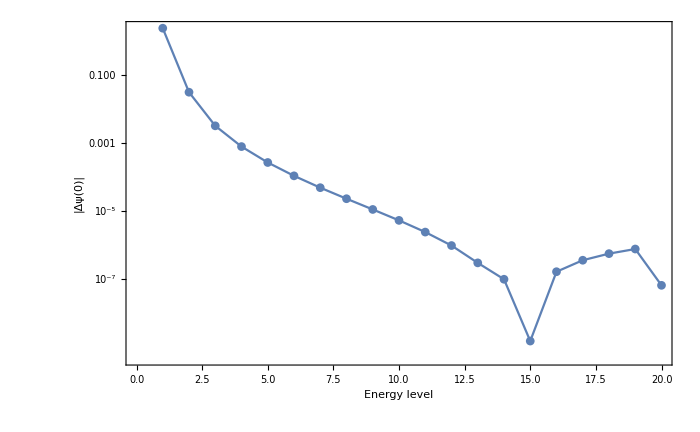

C:\Users\ASUS\OneDrive\Documents\Test_6\psir1.eps

```mathematica
ListLogPlot[Table[Mean[Table[Abs[(ψrfun[r0][n]-NLimit[efV[[n]]/(√(4π)r),r->r0])/NLimit[efV[[n]]/(√(4π)r),r->r0]],{r0,0,1,0.001}]],{n,1,20}],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->700,FrameLabel->Reverse@{"|Δψ(0)|","Energy level"},RotateLabel->True]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\psir1.eps",%]
```

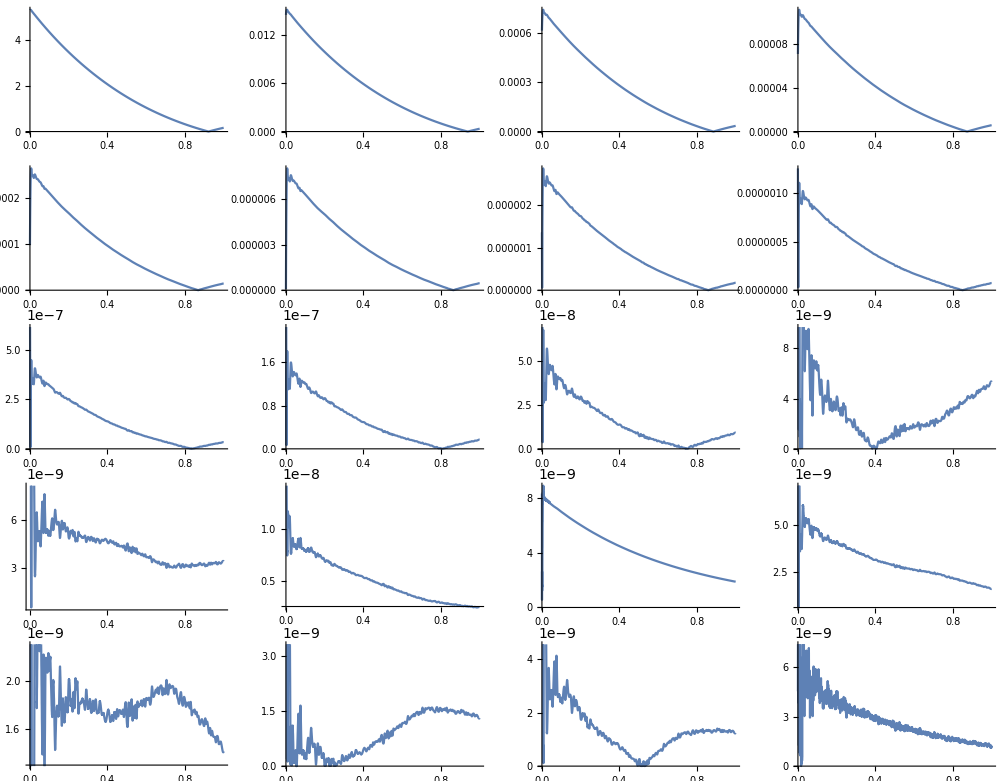

C:\Users\ASUS\OneDrive\Documents\Test_6\psir.eps

```mathematica
GraphicsGrid@Partition[Table[Plot[{Abs[ψrfun[r][n]-efV[[n]]/(√(4π)r)]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],4]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\psir.eps",%]
```

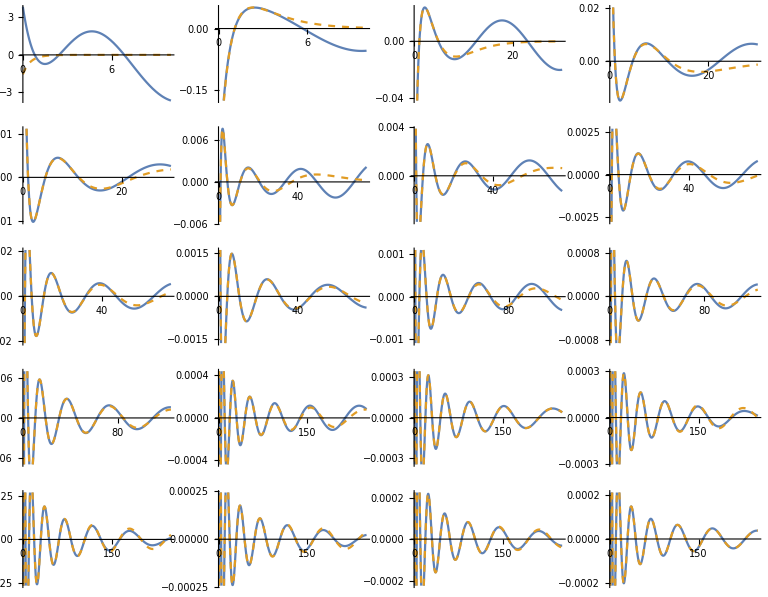

C:\Users\ASUS\OneDrive\Documents\Test_6\psir_2.eps

```mathematica
GraphicsGrid@Partition[Table[Plot[{ψrfun[r][n],efV[[n]]/(√(4π)r)},{r,0,Which[n<3,10,2<n<6,30,5<n<11,75,10<n<14,125,13<n<21,250]},PlotStyle->{{},{Dashed}},ImageSize->175],{n,1,20}],4]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\psir_2.eps",%]
```